To start, motion in the orbit reference frame:

```mathematica
xp = {a, e, f} ↦ (a (1 - e^2)/(1 + e Cos[f])) Cos[f];
yp= {a, e, f} ↦ (a (1 - e^2)/(1 + e Cos[f])) Sin[f];
zp= {a, e, f} ↦ 0;

Manipulate[
Show[
ParametricPlot[{ xp[a, e, fp], yp[a, e, fp]},{fp, 0, 2Pi}, PlotRange->{{-5,5},{-5,5}}],
ListPlot[{{xp[a, e, f], yp[a, e, f]}}, PlotMarkers->{Automatic, Large}]
],
{{a,3}, 1, 5}, {e, 0, 1},{f,0,2Pi}]
```

Now, translating that into the observer’s sky frame:
(note: Ω is set to 180 deg following Winn 2010, which makes it transit left to right at f=90)

```mathematica
rotx = {v, ϕ} ↦{{1,0,0},{0, Cos[ϕ], -Sin[ϕ]}, {0, Sin[ϕ], Cos[ϕ]}}.v;
rotz = {v, ϕ} ↦{{Cos[ϕ], -Sin[ϕ], 0},{Sin[ϕ], Cos[ϕ], 0},{0,0,1}}.v;
roty = {v, ϕ} ↦ {{Cos[ϕ], 0, Sin[ϕ]},{0,1,0},{-Sin[ϕ],0, Cos[ϕ]}}.v;

(* v is a vector in the orbital frame, moved to a vector in sky frame *)
orb2SkyTransform = {v, ω, i, Ω} ↦rotz[rotx[rotz[v, ω], i], Ω];
(* v is a vector in the sky frame, moved to a vector in the orbit frame. Not used here, but we need it later *)
sky2OrbTransform = {v, ω, i, Ω} ↦ rotz[rotx[rotz[v, -Ω], -i], -ω];

(* just to confirm these really are inverses of each other, print this *)
Simplify[orb2SkyTransform[sky2OrbTransform[{x, y, z}, ω, i, Ω],ω, i, Ω ]]


skypos = {a, e, f, ω, i, Ω}↦orb2SkyTransform[{xp[a, e,f], yp[a, e,f], zp[a, e,f]}, ω, i, Ω];

Manipulate[
Show[
ParametricPlot3D[skypos[a,e,ft,ω, i, Ω], {ft, 0, 2Pi}, ViewPoint->{0,0,∞}, PlotRange->{{-5,5},{-5,5},{-5,5}}
],
Graphics3D[{Yellow, Sphere[{0,0,0}, 1],
Red, Sphere[skypos[a,e,f,ω, i, Ω], 0.5]}]
],
{{a,3},1,5}, {e, 0, 1}, {f, 0, 2Pi}, {ω, 0, 2 Pi}, {i, 0, Pi}, {{Ω, Pi}, 0, 2 Pi}]
```

{x,y,z}

Setting that aside, need to describe the oblate spheroid:

```mathematica
Manipulate[
ContourPlot3D[(α^2/a^2 + β^2/(a^2(1-f2)^2)+γ^2/(a^2(1-f1)^2))==1 ,{α,-3,3},{β,-3,3},{γ,-3,3}],
{a,1.5,3},{f1,0,0.4},{f2, 0, 0.4}]
```

We' ll define obliquity ϕ as a rotation about the y axis in the orbital plane of the planet when it' s at periapsis . This means when it' s off to the right from its perspective, where a positive ϕ tips the North pole away from the star. We' ll define precession θ as a rotation around the z axis, again in the planet’s un-rotated plane. So, {ϕ, θ} = {Pi/6, 0} is a 30 deg obliquity with winter solstice at periapsis, and {Pi/6, Pi/2} is an equinox with the North pole leaning a little ways up the y axis. Remember, once we assert that Ω is 180, it will point slightly down the y axis in the sky plane. 

The goal is to get a transformation that takes points in the sky frame and expresses them in the planet’s equatorial frame. If we can do that, we can plug these new coords into the expression of the ellipsoid

```mathematica
(* c is the location of the center of the planet, v is the point in the orbital frame that you want to take in to the planet's equitorial plane *)
orb2PlanetTransform = {v, ϕ, θ} ↦ roty[rotz[v, -θ], -ϕ];
planet2OrbTransform = {v, ϕ, θ} ↦ rotz[roty[v, ϕ], θ];

w = orb2PlanetTransform[sky2OrbTransform[{x, y, z}, ω, i, Ω]-{xp[a,e,f], yp[a,e,f], zp[a, e, f]}, ϕ, θ];
planet = (w[[1]]^2/r^2 + w[[2]]^2/(r^2(1-f2)^2)+w[[3]]^2/(r^2(1-f1)^2))

w = orb2PlanetTransform[sky2OrbTransform[{x, y, z}, ω, i, Ω], ϕs, θs];
star = (w[[1]]^2/rs^2 + w[[2]]^2/rs^2+w[[3]]^2/(rs^2(1-f1s)^2))
```

1/((1-f2)^2 r^2)(Cos[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))-Sin[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω]))))^2+1/r^2(-Sin[ϕ] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Cos[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2+1/((1-f1)^2 r^2)(Cos[ϕ] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Sin[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2

1/rs^2(Cos[θs] (-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))-Sin[θs] (Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω]))))^2+1/rs^2(-Sin[ϕs] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Cos[ϕs] (Sin[θs] (-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θs] (Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2+1/((1-f1s)^2 rs^2)(Cos[ϕs] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Sin[ϕs] (Sin[θs] (-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θs] (Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2

```mathematica
Manipulate[
Show[
ContourPlot3D[1/((1-f2)^2 r^2)(Cos[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))-Sin[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω]))))^2+1/r^2(-Sin[ϕ] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Cos[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2+1/((1-f1)^2 r^2)(Cos[ϕ] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Sin[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2==1, {x, -5, 5}, {y, -5, 5}, {z, -5, 5}, 
ViewPoint->{0,0,∞},PlotRange->{{-5,5},{-5,5},{-5,5}}],

ContourPlot3D[1/rs^2(Cos[θs] (-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))-Sin[θs] (Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω]))))^2+1/rs^2(-Sin[ϕs] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Cos[ϕs] (Sin[θs] (-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θs] (Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2+1/((1-f1s)^2 rs^2)(Cos[ϕs] (z Cos[i]-Sin[i] (y Cos[Ω]-x Sin[Ω]))+Sin[ϕs] (Sin[θs] (-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))+Cos[θs] (Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (z Sin[i]+Cos[i] (y Cos[Ω]-x Sin[Ω])))))^2==1, {x, -5, 5}, {y, -5, 5}, {z, -5, 5}, 
ViewPoint->{0,0,∞},PlotRange->{{-5,5},{-5,5},{-5,5}}],

ParametricPlot3D[skypos[a,e,ft,ω, i, Ω], {ft, 0, 2Pi}, ViewPoint->{0,0,∞}, PlotRange->{{-5,5},{-5,5},{-5,5}}
]


],

{{a,3}, 1, 5}, {e, 0, 1}, {f,0, 2Pi}, {ω,0, 2Pi}, {i, 0, Pi}, {{Ω,Pi},0, 2Pi}, {ϕ,0, Pi}, {θ, 0, 2 Pi},{{r,0.5},0.1,2}, {f1,0, 0.4}, {f2, 0, 0.4}, {rs,1,3}, {f1s,0,0.5}, {ϕs,0,Pi}, {θs, 0, 2Pi}]
```

Now we need to actually see what this would look like projected on the sky, not in 3D. We’re looking down the z axis, so the boundary will be orthogonal to the normal of the planet’s surface. We can get that by setting the z derivative to zero, solving for Z where that happens as a function of x and y, then plug that back into the original planet equation to get the ellipse that’s a function of just x and y. This shape both lives in the boundary plane and hugs the planet’s surface.

-6.22615-0.706914 x+1.34187 y+8.2861 z

{z→0.120684 (5.71904-0.706914 (-0.717356-1. x)-1.34187 y)}

2.42088+4.8432 x^2+x (6.83713-3.20113 y)-1.8062 y+7.03821 y^2

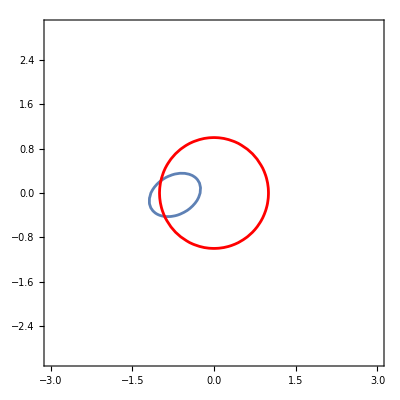

```mathematica
params = {a-> 1, e-> 0, f-> Pi/2-0.8, ω-> 0, Ω->Pi, i-> Pi/2-0.05, ϕ-> 0.5, θ->0.3,r-> 0.5, f1-> 0.3, f2->0};

Simplify[D[planet, z] /.params]

zsol = Solve[(D[planet, z] /. params) ==0, z][[1]]

outline = Simplify[planet /.params/. zsol]


Show[
ContourPlot[outline==1, {x,-5, 5}, {y,-5,5}, PlotRange->{{-3,3}, {-3,3}}],
ContourPlot[x^2 + y^2 == 1, {x,-5, 5}, {y,-5,5}, PlotRange->{{-3,3}, {-3,3}}, ContourStyle->Red]
]
```

The general form is super messy, but it does evaluate quickly:

```mathematica
zsol = Solve[D[planet, z] ==0, z][[1]];
planet /. zsol
```

```mathematica
Manipulate[
ContourPlot[1/((1-f2)^2 r^2)((Cos[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-(2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/r^2-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/((1-f1)^2 r^2)-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2))))-Sin[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-(2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/r^2-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/((1-f1)^2 r^2)-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2))))))^2+1/r^2((-Sin[ϕ] (-Sin[i] (y Cos[Ω]-x Sin[Ω])+(Cos[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-(2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/r^2-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/((1-f1)^2 r^2)-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)))+Cos[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2))))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)))))))^2+1/((1-f1)^2 r^2)((Cos[ϕ] (-Sin[i] (y Cos[Ω]-x Sin[Ω])+(Cos[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-(2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/r^2-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω]))/((1-f1)^2 r^2)-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)))+Sin[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2))))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/(r^2 (1+e Cos[f]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-(2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+(2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)+(2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω]))/((1-f2)^2 r^2)-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/((2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)-(2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2)+(2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2-(2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/r^2+(2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)+(2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2)))))))^2==1, {x,-5, 5}, {y,-5,5}, PlotRange->{{-3,3}, {-3,3}}],
{{a,3}, 1, 5}, {e, 0, 1}, {f,0, 2Pi}, {ω,0, 2Pi}, {i, 0, Pi}, {{Ω,Pi},0, 2Pi}, {ϕ,0, Pi}, {θ, 0, 2 Pi},{r,1,2}, {f1,0, 0.4}, {f2, 0, 0.4}]
```

```mathematica
Simplify[1/((1-f2)^2 r^2)((Cos[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))))-Sin[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))))))^2+1/r^2((-Sin[ϕ] (-Sin[i] (y Cos[Ω]-x Sin[Ω])+(Cos[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))))+Cos[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))))))))^2+1/((1-f1)^2 r^2)((Cos[ϕ] (-Sin[i] (y Cos[Ω]-x Sin[Ω])+(Cos[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))))+Sin[ϕ] (Sin[θ] (-(a (1-e^2) Sin[f])/(1+e Cos[f])-Sin[ω] (x Cos[Ω]+y Sin[Ω])+Cos[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))))+Cos[θ] (-(a (1-e^2) Cos[f])/(1+e Cos[f])+Cos[ω] (x Cos[Ω]+y Sin[Ω])+Sin[ω] (Cos[i] (y Cos[Ω]-x Sin[Ω])+(Sin[i] ((2 a (1-e^2) Cos[θ] Sin[f] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))-(2 a (1-e^2) Cos[f] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]))/((1-f2)^2 r^2 (1+e Cos[f]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[f] Cos[θ] Cos[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/(r^2 (1+e Cos[f]))2 a (1-e^2) Cos[ϕ] Sin[f] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+(2 a (1-e^2) Cos[f] Cos[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))+(2 a (1-e^2) Sin[f] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])))/((1-f1)^2 r^2 (1+e Cos[f]))-1/((1-f2)^2 r^2)2 Cos[i] Cos[θ] Cos[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[ϕ] Cos[ω] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Sin[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/r^2 2 Cos[i] Cos[θ] Cos[ϕ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f1)^2 r^2)2 Cos[ϕ] Sin[i] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[ω] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[i] Cos[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (y Cos[Ω]-x Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[ω] Sin[θ] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])+1/((1-f2)^2 r^2)2 Cos[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω]) (x Cos[Ω]+y Sin[Ω])-1/r^2 2 Cos[θ] Cos[ϕ] Cos[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/r^2 2 Cos[ϕ] Sin[θ] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])-1/((1-f1)^2 r^2)2 Cos[θ] Cos[ω] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])+1/((1-f1)^2 r^2)2 Sin[θ] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω])) (x Cos[Ω]+y Sin[Ω])))/(1/((1-f2)^2 r^2)2 Cos[θ] Cos[ω] Sin[i] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])-1/((1-f2)^2 r^2)2 Sin[i] Sin[θ] Sin[ω] (Cos[θ] Cos[ω] Sin[i]-Sin[i] Sin[θ] Sin[ω])+1/r^2 2 Cos[ϕ] Cos[ω] Sin[i] Sin[θ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))-1/r^2 2 Cos[i] Sin[ϕ] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/r^2 2 Cos[θ] Cos[ϕ] Sin[i] Sin[ω] (-Cos[i] Sin[ϕ]+Cos[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[i] Cos[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[ω] Sin[i] Sin[θ] Sin[ϕ] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))+1/((1-f1)^2 r^2)2 Cos[θ] Sin[i] Sin[ϕ] Sin[ω] (Cos[i] Cos[ϕ]+Sin[ϕ] (Cos[ω] Sin[i] Sin[θ]+Cos[θ] Sin[i] Sin[ω]))))))))^2 /. {a-> 1.1232, e-> 0.4, f-> Pi/2-0.424, ω-> 4.12, Ω->Pi, i-> Pi/2-0.5, ϕ-> 1, θ->2,r-> 0.5, f1-> 0.3, f2->0.42}]
```

2.39514+6.82523 x^2+x (6.96045-3.44755 y)-5.51621 y+6.12568 y^2